# 几何体维度矩阵

{8,12,11,9,19,20,1,12,0,18}

```mathematica
Sort[{8,12,11,9,19,20,1,12,0,18}]
```

{0,1,8,9,11,12,12,18,19,20}

```mathematica
Mean[{8,12,11,9,19,20,1,12,0,18}]
```

11

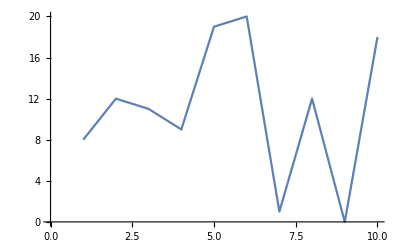

```mathematica
ListLinePlot[{8,12,11,9,19,20,1,12,0,18}]
```

```mathematica
sphere={Cos[u]Sin[v],Sin[u]Sin[v],Cos[v]};
ParametricPlot3D[sphere,{u,0,2π},{v,0,π}]
```

-Graphics3D-

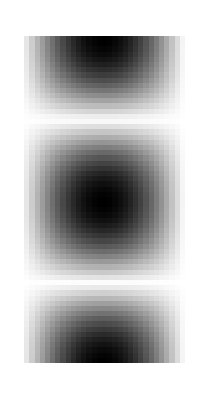
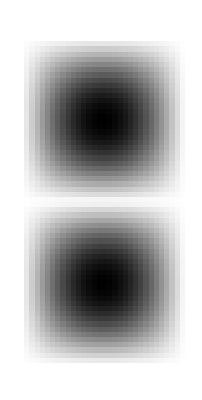
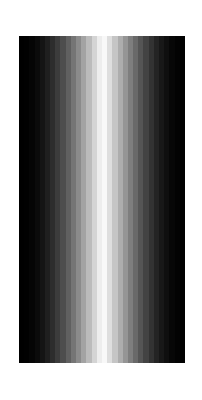

```mathematica
ArrayPlot[Table[#,{u,0,2π,0.1},{v,0,π,0.1}]]&/@sphere
```

```mathematica
torus={Cos[u](1+0.3Sin[v]),Sin[u](1+0.3Sin[v]),0.3Cos[v]};
ParametricPlot3D[torus,{u,0,2π},{v,0,2π}]
```

-Graphics3D-

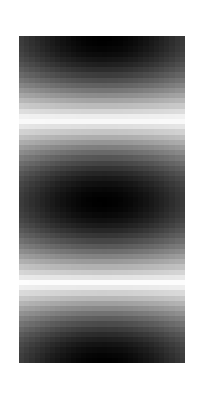
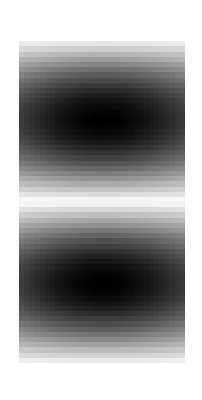
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[Table[#,{u,0,2π,0.1},{v,0,π,0.1}]]&/@torus
```

```mathematica
c=KnotData[{3,1},"SpaceCurve"];n=Simplify@FrenetSerretSystem[c[u],u][[-1,2;;]];
trefoil:={3c[u]+RotationMatrix[7u].{Cos[v],Sin[v]}.n(1+.3Cos[3v]+0.3Cos[6v])}
ParametricPlot3D[trefoil,{u,0,2Pi},{v,0,2Pi},PlotPoints->50,ColorFunction->(Hue[#5]&),Mesh->None]
```

-Graphics3D-

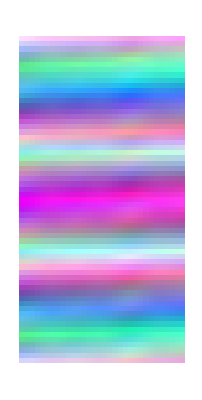

```mathematica
ArrayPlot[Table[#,{u,0,2π,0.1},{v,0,π,0.1}]]&/@trefoil
```

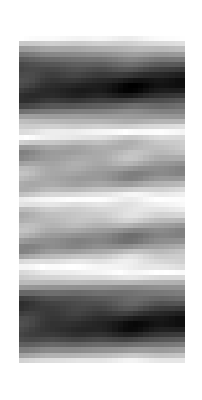
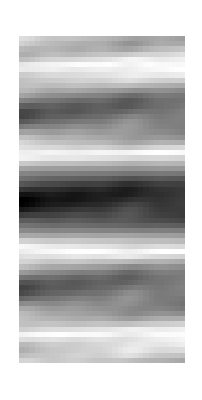
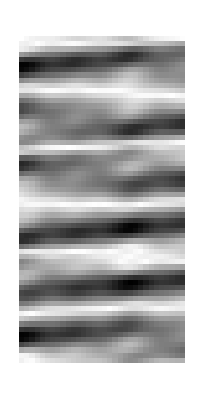

```mathematica
ArrayPlot[Table[#,{u,0,2π,0.1},{v,0,π,0.1}]]&/@trefoil[[1]]
```

```mathematica
dataPts=Table[trefoil[[1]],{u,0,2π,0.05},{v,0,2π,0.2}];
```

```mathematica
ParametricPlot3D[dataPts[[Round[u,0.1]+1,Round[v,0.1]+1]],{u,0,2π},{v,0,π}]
```

-Graphics3D-

```mathematica
ListPlot3D[dataPts,InterpolationOrder->4]
```

-Graphics3D-

```mathematica
ListPlot3D[dataPtsᵀ,InterpolationOrder->3]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataPts]
```

-Graphics3D-

```mathematica
ListPointPlot3D[dataPtsᵀ]
```

-Graphics3D-

```mathematica
ListPointPlot3D[Flatten[dataPts,1]]
```

-Graphics3D-